# One Iteration of Approximation in Policy Space for Betting on Multiple Rounds of Coin Flips

## Supplemental material for Sec. 5.10.

## Import Directory

```mathematica
importDirectory=ParentDirectory[NotebookDirectory[]]<>"/files/coin";
```

```mathematica
SetDirectory@importDirectory
```

```mathematica
Import["parameters.txt"]
```

Max number of chips: 100
Probability of heads: 0.75

```mathematica
maxNumberOfChips=100;
p=0.75;
```

## Utility function

```mathematica
U[x_,a_,c_]:=Tanh[a(x-c)]
```

```mathematica
Manipulate[
plotOfUtilityFunction=Plot[U[x,a,c],{x,0,maxNumberOfChips},
PlotLabel->Style["Utility Function",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Chips",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black
],
{a,0.01,1},{c,0,100}]
```

### Absolute risk aversion

```mathematica
A[x_,a_,c_]=-D[#, x,x]/D[#, x]&@U[x,a,c]
```

2 a Tanh[a (-c+x)]

```mathematica
Manipulate[
Plot[A[x,a,c],{x,0,maxNumberOfChips}],
{a,0.01,1},{c,0,100}]
```

### Relative risk aversion

```mathematica
R[x_,a_,c_]=x A[x,a,c]
```

2 a x Tanh[a (-c+x)]

```mathematica
Manipulate[
plotOfRelativeRiskAversion=Plot[R[x,a,c],{x,0,maxNumberOfChips},
PlotLabel->Style["Relative Risk Aversion",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Chips",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black],
{a,0.01,1},{c,0,100}]
```

## Playbooks

### Final decision

```mathematica
finalDecisionExact=Flatten@Import["finalDecision_exact.csv"];
```

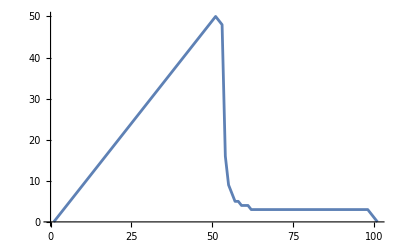

```mathematica
ListLinePlot[finalDecisionExact]
```

```mathematica
finalDecisionApproximate=Flatten@Import["finalDecision_approximate.csv"];
```

```mathematica
ListLinePlot[finalDecisionApproximate]
```

-Graphics-

Those should agree:

```mathematica
finalDecisionApproximate-finalDecisionExact
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Penultimate decision

```mathematica
penultimateDecisionExact=Flatten@Import["penultimateDecision_exact.csv"];
```

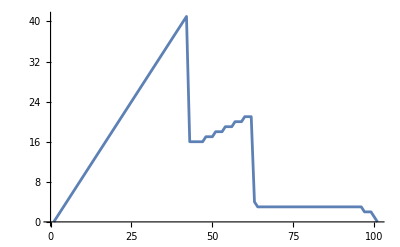

```mathematica
ListLinePlot[penultimateDecisionExact]
```

```mathematica
penultimateDecisionApproximate=Flatten@Import["penultimateDecision_approximate.csv"];
```

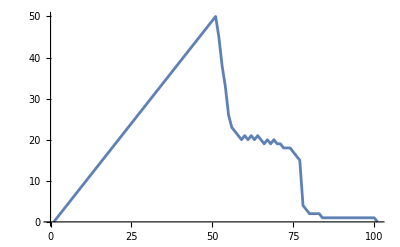

```mathematica
ListLinePlot[penultimateDecisionApproximate]
```

```mathematica
penultimateDecisionApproximate-penultimateDecisionExact
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,26,27,28,29,30,30,31,32,32,27,20,14,7,4,2,1,0,0,-1,0,16,18,17,16,17,16,17,16,16,15,15,15,14,13,12,1,0,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,0,0}

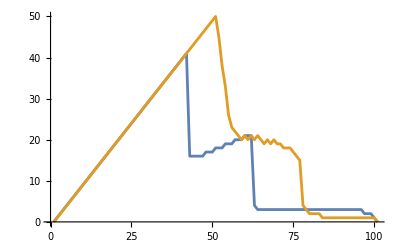

```mathematica
ListLinePlot[{penultimateDecisionExact,penultimateDecisionApproximate},PlotRange->All]
```

### First decision

```mathematica
firstDecisionExact=Flatten@Import["firstDecision_exact.csv"];
```

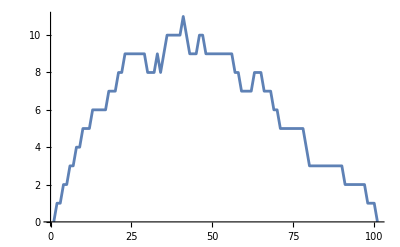

```mathematica
ListLinePlot[firstDecisionExact]
```

```mathematica
firstDecisionApproximate=Flatten@Import["firstDecision_approximate.csv"];
```

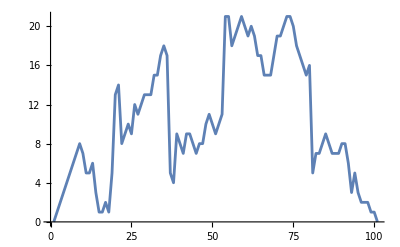

```mathematica
ListLinePlot[firstDecisionApproximate]
```

```mathematica
firstDecisionApproximate-firstDecisionExact
```

{0,0,1,1,2,2,3,3,4,2,0,0,0,-3,-5,-5,-4,-6,-2,6,6,0,0,1,0,3,2,3,4,5,5,7,6,9,9,7,-5,-6,-1,-2,-4,-1,0,-1,-2,-2,-2,1,2,1,0,1,2,12,12,9,11,12,14,13,12,13,11,9,9,8,8,8,11,13,14,15,16,16,15,13,12,11,11,13,2,4,4,5,6,5,4,4,4,5,6,4,1,3,1,0,0,1,0,0,0}

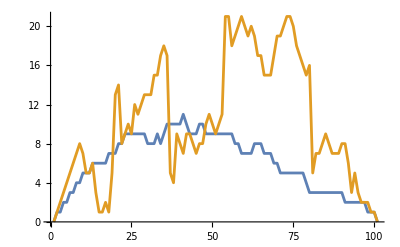

```mathematica
ListLinePlot[{firstDecisionExact,firstDecisionApproximate},PlotRange->All]
```

## Comparison with Log Policy

### Log Policy

```mathematica
Table[(2p-1)x,{x,0,maxNumberOfChips}];
```

```mathematica
ε=10^-4;
```

```mathematica
SetPrecision[#,4]&/@Table[NMaximize[{p Log[x+y+ε]+(1-p)Log[x-y+ε],0<=y<=Min[x,maxNumberOfChips-x]},y],{x,0,maxNumberOfChips}];
```

```mathematica
logPolicy=SetPrecision[#,4]&/@Table[NArgMax[{p Log[x+y+ε]+(1-p)Log[x-y+ε],0<=y<=Min[x,maxNumberOfChips-x]},y],{x,0,maxNumberOfChips}]
```

{0,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.,32.,31.,30.,29.,28.,27.,26.,25.,24.,23.,22.,21.,20.,19.,18.,17.,16.,15.,14.,13.,12.,11.,10.,9.,8.,7.,6.,5.,4.,3.,2.,1.,-0.00008647}

### Plots

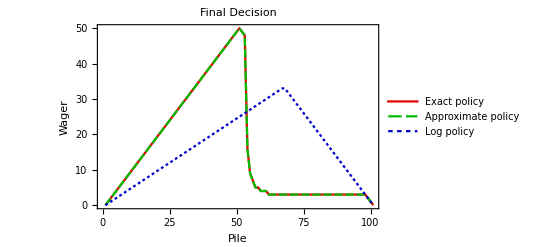

```mathematica
plotOfFinalDecision=ListLinePlot[{finalDecisionExact,finalDecisionApproximate,logPolicy},
PlotRange->All,
PlotLabel->Style["Final Decision",FontSize->13,FontColor->Black],
PlotLegends->{"Exact policy","Approximate policy","Log policy"},
PlotTheme->"Monochrome",
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,12],
FrameLabel->{Style["Pile",FontSize->12],Style["Wager",FontSize->12]},
PlotMarkers->None,
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.75,0],
RGBColor[0,0,0.8]
}]
```

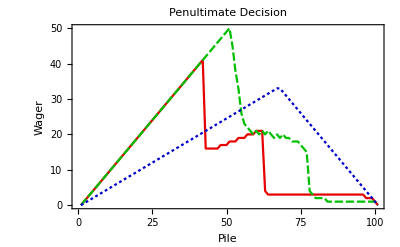

```mathematica
plotOfPenultimateDecision=ListLinePlot[{penultimateDecisionExact,penultimateDecisionApproximate,logPolicy},
PlotRange->All,
PlotLabel->Style["Penultimate Decision",FontSize->13,FontColor->Black],
(*PlotLegends->{"Exact policy","Approximate policy","Log policy"},*)
PlotTheme->"Monochrome",
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,12],
FrameLabel->{Style["Pile",FontSize->12],Style["Wager",FontSize->12]},
PlotMarkers->None,
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.75,0],
RGBColor[0,0,0.8]
}]
```

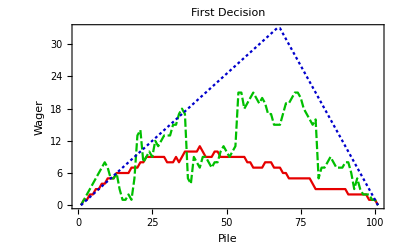

```mathematica
plotOfFirstDecision=ListLinePlot[{firstDecisionExact,firstDecisionApproximate,logPolicy},
PlotRange->All,
PlotLabel->Style["First Decision",FontSize->13,FontColor->Black],
(*PlotLegends->{"Exact policy","Approximate policy","Log policy"},*)
PlotTheme->"Monochrome",
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,12],
FrameLabel->{Style["Pile",FontSize->12],Style["Wager",FontSize->12]},
PlotMarkers->None,
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.75,0],
RGBColor[0,0,0.8]
}]
```

## Write Graphs to Storage

### Export Directory

```mathematica
exportDirectory=NotebookDirectory[]<>"/output/coin";
```

```mathematica
SetDirectory@exportDirectory
```

### Utility function

```mathematica
Export["tanhUtility.pdf",
plotOfUtilityFunction]
```

tanhUtility.pdf

```mathematica
Export["tanhRiskAversion.pdf",
plotOfRelativeRiskAversion]
```

tanhRiskAversion.pdf

### Playbooks

```mathematica
Export["approximationInPolicySpace_finalDecision.pdf",
plotOfFinalDecision]
```

approximationInPolicySpace_finalDecision.pdf

```mathematica
Export["approximationInPolicySpace_penultimateDecision.pdf",
plotOfPenultimateDecision]
```

approximationInPolicySpace_penultimateDecision.pdf

```mathematica
Export["approximationInPolicySpace_firstDecision.pdf",
plotOfFirstDecision]
```

approximationInPolicySpace_firstDecision.pdf